(100 √(2/π) Sin[w])/w

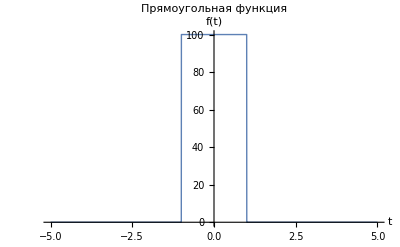

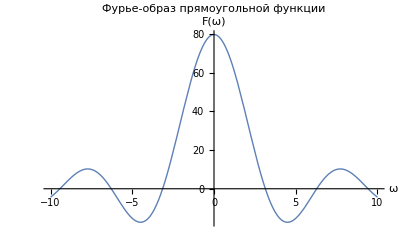

20000

20000

True

```mathematica
f[t_,a_,b_]:=Piecewise[{{a,Abs[t]≤b},{0,Abs[t]>b}}]

a=100;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Прямоугольная функция",Exclusions->None]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ прямоугольной функции"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

energyTimeDomain==energyFrequencyDomain
```

-(ⅇ^(-2 ⅈ w) (-1+ⅇ^(2 ⅈ w))^2)/(2 √(2 π) w^2)

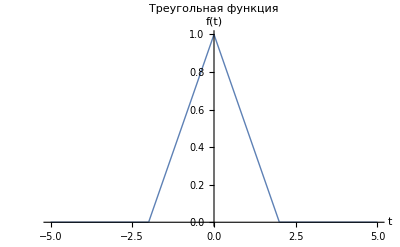

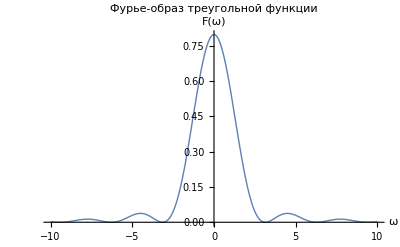

4/3

4/3

True

```mathematica
f[t_,a_,b_]:=Piecewise[{{a-Abs[a t/b],Abs[t]≤b},{0,Abs[t]>b}}]

a=1;
b=2;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Треугольная функция"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ треугольной функции"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

energyTimeDomain==energyFrequencyDomain
```

5/2 √(π/2) (Sign[1-w]+Sign[1+w])

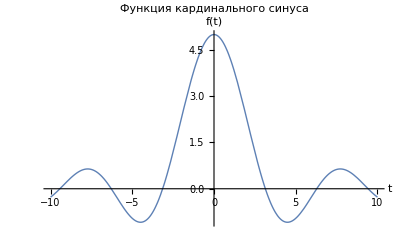

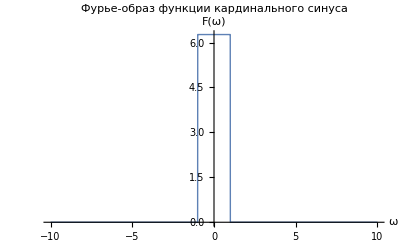

25 π

25 π

True

```mathematica
f[t_,a_,b_]:=a Sinc[b t]

a=5;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция кардинального синуса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции кардинального синуса", Exclusions->None]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

energyTimeDomain==energyFrequencyDomain
```

√2 ⅇ^(-w^2/4)

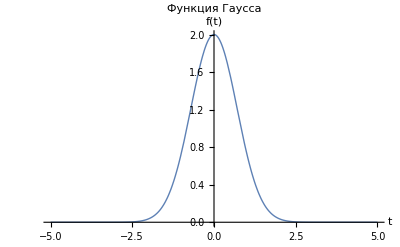

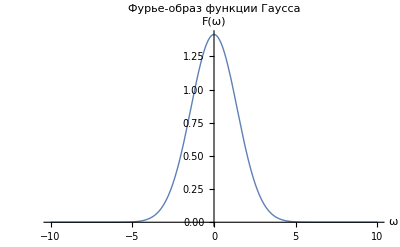

2 √(2 π)

2 √(2 π)

True

```mathematica
f[t_,a_,b_]:=a Exp[-b t^2]

a=2;
b=1;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция Гаусса"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции Гаусса"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

energyTimeDomain==energyFrequencyDomain
```

(2 √(2/π))/(4+w^2)

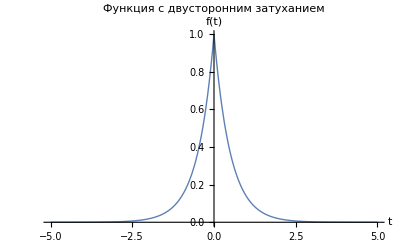

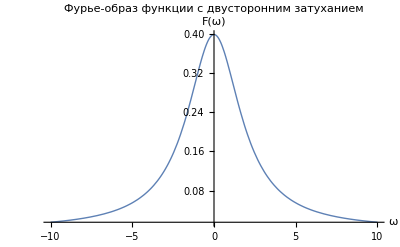

1/2

1/2

True

```mathematica
f[t_,a_,b_]:=a Exp[-b Abs[t]]

a=1;
b=2;

fourier=FourierTransform[f[t,a,b],t,w]

Plot[f[t,a,b],{t,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","f(t)"},PlotLabel->"Функция с двусторонним затуханием"]

Plot[Re[fourier],{w,-10,10},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ω","F(ω)"},PlotLabel->"Фурье-образ функции с двусторонним затуханием"]

energyTimeDomain=Integrate[Abs[f[t,a,b]]^2,{t,-Infinity,Infinity}]

energyFrequencyDomain=Integrate[Abs[fourier]^2,{w,-Infinity,Infinity}]

energyTimeDomain==energyFrequencyDomain
```

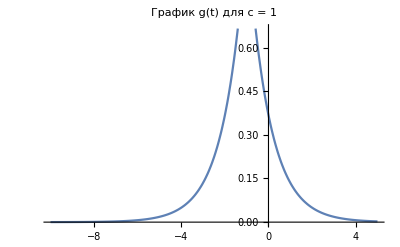
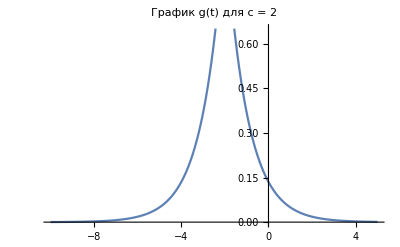
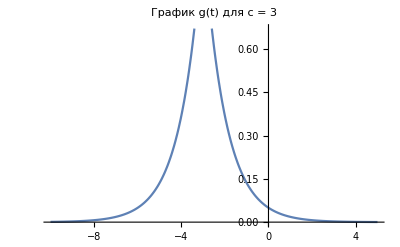

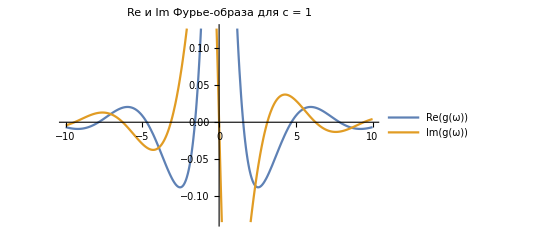
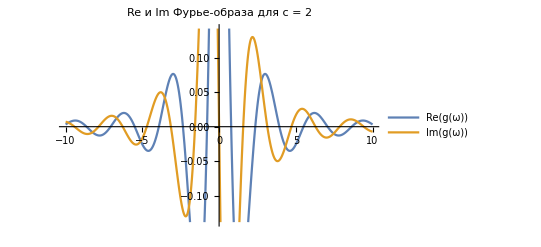
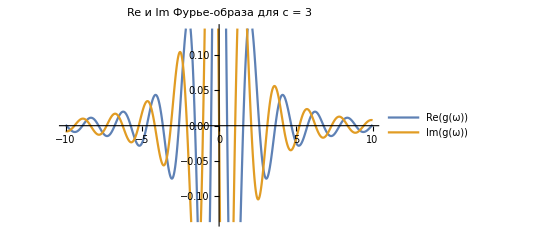

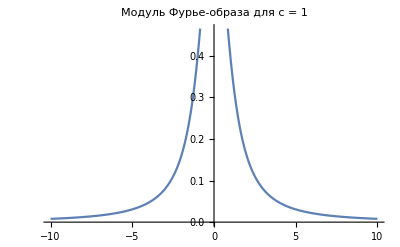
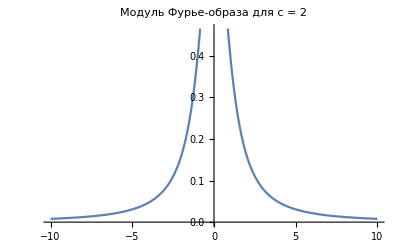

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

ListLinePlot::lpn: Transpose[{AudioTimeStamps[Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]],{{0.,4.01069×10^-11,3.96901×10^-11,3.76073×10^-11,2.90611×10^-11,2.39398×10^-11,3.29224×10^-11,7.54432×10^-11,4.5152×10^-11,2.09849×10^-11,3.93559×10^-11,6.1067×10^-11,«27»,6.84967×10^-10,-2.21453×10^-10,-1.13749×10^-9,-8.11829×10^-10,-1.79799×10^-10,3.50149×10^-10,1.4498×10^-9,2.57442×10^-9,2.17523×10^-9,1.71195×10^-9,3.07982×10^-9,«266062»},{0.,-3.93298×10^-12,«48»,«266062»}}}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {AudioTimeStamps[Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]],{{0.,4.01069×10^-11,3.96901×10^-11,3.76073×10^-11,2.90611×10^-11,2.39398×10^-11,3.29224×10^-11,7.54432×10^-11,4.5152×10^-11,2.09849×10^-11,3.93559×10^-11,6.1067×10^-11,-3.65752×10^-11,«25»,-2.69079×10^-10,6.84967×10^-10,-2.21453×10^-10,-1.13749×10^-9,-8.11829×10^-10,-1.79799×10^-10,3.50149×10^-10,1.4498×10^-9,2.57442×10^-9,2.17523×10^-9,1.71195×10^-9,3.07982×10^-9,«266062»},{«1»}}} cannot be transposed.

Part::partd: Part specification Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,2⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,2⟧,Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,1⟧} cannot be transposed.

ListLinePlot::lpn: Transpose[{Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,2⟧,Audio[/home/eva/Документы/itmo/2_course/chMetods/lab2/audio.mp3,Real32,Appearance→Automatic,AudioOutputDevice→Automatic,SampleRate→44100,SoundVolume→1]⟦1,1⟧}] is not a list of numbers or pairs of numbers.

```mathematica
a=1;
b=1;
f[t_]:=a Exp[-b Abs[t]];

cValues={1,2,3};
g[t_,c_]:=f[t+c];

fourierTransforms=Table[FourierTransform[g[t,c],t,ω],{c,cValues}];

plotsG=Table[Plot[g[t,c],{t,-10,5},PlotLabel->"График g(t) для c = "<>ToString[c]],{c,cValues}]

plotsReIm=Table[Plot[{Re[fourierTransforms[[c]]],Im[fourierTransforms[[c]]]},{ω,-10,10},PlotLegends->{"Re(g(ω))","Im(g(ω))"},PlotLabel->"Re и Im Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]

plotsAbs=Table[Plot[Abs[fourierTransforms[[c]]],{ω,-10,10},PlotLabel->"Модуль Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]
```

```mathematica
ListLinePlot[Transpose[{⟦1,2⟧,⟦1,1⟧}],PlotLabel->"График fx(t)"]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k, Length[t]}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {k,Length[t]}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.